```mathematica
H[s_]:=((s/10)^2+0.1(s/10)+1)(s/2+1)(s/0.1+1)/(((s/4)^2+(s/4)+1)((s/10)^2+0.09(s/10)+1)(s/0.02+1));
H[s]//DisplayForm
```

((1+s/2) (1+10. s) (1+0.01 s+s^2/100))/((1+50. s) (1+0.009 s+s^2/100) (1+s/4+s^2/16))

```mathematica
y[t_]:=InverseLaplaceTransform[1/s*H[s],s,t]
```

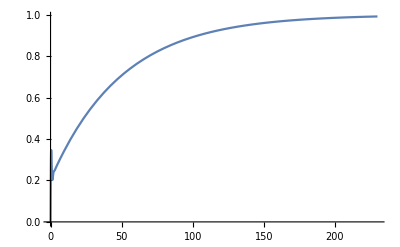

```mathematica
Plot[y[t],{t,0,230}]
```

```mathematica
FindRoot[y[t]==0.99,{t,230}]
```

{t→218.847-3.56053×10^-61 ⅈ}